# Regular graph generation

## Recursively generating graphs, backtracking, pruning.

```mathematica
SetDirectory@NotebookDirectory[];
```

## Straightforward approach

We add edges one-by-one, filtering for non-isomorphic graphs after each addition.
We can only discard disconnected graphs at the last step (this is slow!).

```mathematica
ClearAll@MyCanonicalGraph;
MyCanonicalGraph[g_Graph,d_Integer]:=MyCanonicalGraph[g,d]=
With[{n=VertexCount@g,m=AdjacencyMatrix@g},
Min@Table[FromDigits[Flatten@m⟦p,p⟧,d+1],{p,Permutations@Range@n}]
]
```

```mathematica
ClearAll@GenerateGraphs;
GenerateGraphs[n_Integer,0,d_Integer]:={Graph[Range@n,{}]};
GenerateGraphs[n_Integer,e_Integer,d_Integer]:=GenerateGraphs[n,e,d]=
DeleteDuplicatesBy[
Flatten[
Table[
Block[{tmp},
tmp=d-VertexDegree@g;
EdgeAdd[g,First@#<->Last@#]&/@Select[Subsets[Range@n,{2}],Times@@tmp⟦#⟧>0&]
]
,{g,GenerateGraphs[n,e-1,d]}]
,1]
,MyCanonicalGraph[#,d]&]
```

```mathematica
Select[GenerateGraphs[4,8,4],ConnectedGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-}

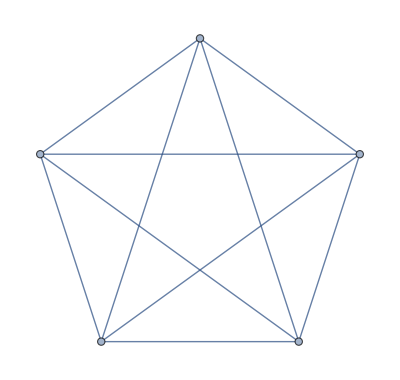
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[GenerateGraphs[5,10,4],ConnectedGraphQ]
```

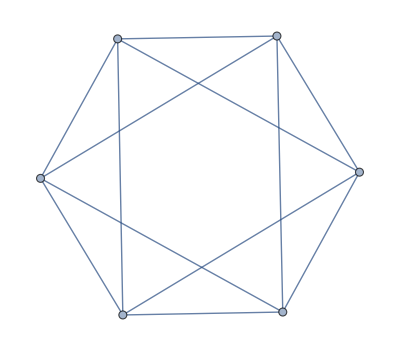
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[GenerateGraphs[6,12,4],ConnectedGraphQ]
```

```mathematica
ClearAll@GenerateGraphs2;
GenerateGraphs2[n_Integer,0,d_Integer]:={Graph[Range@n,{}]};
GenerateGraphs2[n_Integer,e_Integer,d_Integer]:=GenerateGraphs2[n,e,d]=
Block[{glist},
glist=Flatten[
Table[
Block[{tmp},
tmp=d-VertexDegree@g;
EdgeAdd[g,First@#<->Last@#]&/@Select[Subsets[Range@n,{2}],Times@@tmp⟦#⟧>0&]
]
,{g,GenerateGraphs2[n,e-1,d]}]
,1];
Print["graphs with e = ",e,": ",Length@glist];
DeleteDuplicatesBy[glist,MyCanonicalGraph[#,d]&]
]
```

### We can also try to merge two graphs of degree at most 2 to obtain a single graph of degree at most 4

```mathematica
With[{n=8,d=2},
Do[
Print["There are ",Length@GenerateGraphs[n,e,d]," graphs with ",n," vertices, ",e," edges and degree at most ",d];
,{e,d n/2}]
]
```

There are 1 graphs with 8 vertices, 1 edges and degree at most 2

There are 3 graphs with 8 vertices, 2 edges and degree at most 2

There are 5 graphs with 8 vertices, 3 edges and degree at most 2

There are 10 graphs with 8 vertices, 4 edges and degree at most 2

There are 14 graphs with 8 vertices, 5 edges and degree at most 2

There are 19 graphs with 8 vertices, 6 edges and degree at most 2

There are 15 graphs with 8 vertices, 7 edges and degree at most 2

There are 7 graphs with 8 vertices, 8 edges and degree at most 2

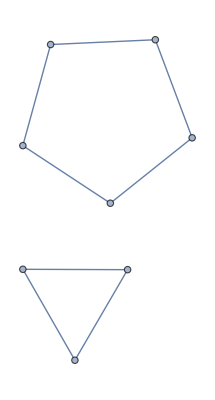
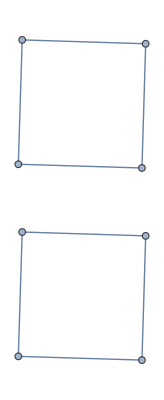
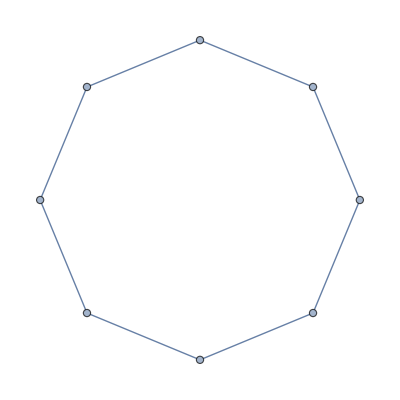
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GenerateGraphs[8,8,2]
```

```mathematica
GraphPermutations[g_Graph]:=
With[{n=VertexCount@g,m=AdjacencyMatrix@g},
Table[AdjacencyGraph@m⟦p,p⟧,{p,Permutations@Range@n}]
]
```

```mathematica
Block[{glist=GenerateGraphs[8,8,2]},
glist=Flatten@Table[Graph@Join[EdgeList@g1,EdgeList@g2p],{g1,glist},{g2,glist},{g2p,GraphPermutations@g2}];
Print@Length@glist;
glist=Select[glist,ConnectedGraphQ];
Print@Length@glist;
glist=DeleteDuplicates@glist;
Print@Length@glist;
glist=DeleteDuplicatesBy[glist,MyCanonicalGraph[#,4]&];
Print@Length@glist;
glist
];
```

1975680

1865040

42208

204

We found  there are 204 graphs which are 4-regular and have 8 vertices, but this was painful!

## Inflating connected graphs

We may alternatively start by constructing all the connected graphs with k vertices, and then add repeated edges until they become 4-regular.

```mathematica
ClearAll@PreSubsets;
PreSubsets[n_Integer,d_Integer]:=PreSubsets[n,d]=Subsets[Range[n-1],{1,Min[d,n-1]}];
```

```mathematica
MyDeleteDuplicates[glist_]:=Flatten[DeleteDuplicates[#,IsomorphicGraphQ]&/@GatherBy[glist,Sort@VertexDegree@#&]]
```

```mathematica
ClearAll@GenConn;
GenConn[1,d_Integer]:={Graph[{1},{}]};
GenConn[n_Integer,d_Integer]:=GenConn[n,d]=
MyDeleteDuplicates@Select[
Flatten[Table[
EdgeAdd[g,#]&/@Map[n<->#&,PreSubsets[n,d],{2}]
,{g,GenConn[n-1,d]}],1]
,Max@VertexDegree@#≤d&]
GenConn[n_Integer,e_Integer,d_Integer]:=GenConn[n,e,d]=Select[GenConn[n,d],EdgeCount@#==e&];
```

```mathematica
Length@GenConn[8,4]//AbsoluteTiming
```

{13.7562,1929}

```mathematica
ClearAll@GenerateGraphs;
GenerateGraphs[n_Integer,e_Integer,d_Integer]/;e==n-1:=GenConn[n,e,d];
GenerateGraphs[n_Integer,e_Integer,d_Integer]:=GenerateGraphs[n,e,d]=
DeleteDuplicatesBy[
Select[
Flatten[Table[
EdgeAdd[g,#]&/@DeleteDuplicates@EdgeList@g
,{g,GenerateGraphs[n,e-1,d]}],1]
,Max@VertexDegree@#≤d&]~Join~GenConn[n,e,d]
,MyCanonicalGraph[#,d]&]
```

```mathematica
Do[Print@Length@GenerateGraphs[8,e,4],{e,7,16}]
```

18

139

654

2082

4679

7437

7982

5308

1804

204

```mathematica
Export["Connected4RegularGraphs.m",Table[GenerateGraphs[n,2n,4],{n,2,8}]]
```

Connected4RegularGraphs.m

A figure for the problem statement

```mathematica
Export["RegularGraphs.pdf",Row@Flatten@Table[GenerateGraphs[n,2n,4],{n,2,4}]]
```

## Graph evaluation

### First definition

```mathematica
ClearAll@Vertex;
Vertex[id_,{a_,b_,c_,d_}]:=δ[i[id,a],i[id,b]]δ[i[id,c],i[id,d]]δ[j[id,a],j[id,c]]δ[j[id,b],j[id,d]]δ[k[id,a],k[id,d]]δ[k[id,b],k[id,c]];
```

```mathematica
Prop[{id1_,a_},{id2_,b_}]:=δ[i[id1,a],i[id2,b]]δ[j[id1,a],j[id2,b]]δ[k[id1,a],k[id2,b]];
```

```mathematica
ClearAll@δ;
SetAttributes[δ,Orderless];
δ/:δ[x_,y_]δ[y_,z_]:=δ[x,z];
δ/:δ[x_,y_]^2:=n;
δ/:δ[x_,x_]:=n;
```

### Better definition

```mathematica
ClearAll@Vertex;
Vertex[id_,{a_,b_,c_,d_}]:=δv[i[id,a],i[id,b]]δv[i[id,c],i[id,d]]δv[j[id,a],j[id,c]]δv[j[id,b],j[id,d]]δv[k[id,a],k[id,d]]δv[k[id,b],k[id,c]];
```

```mathematica
Prop[{id1_,a_},{id2_,b_}]:=δp[i[id1,a],i[id2,b]]δp[j[id1,a],j[id2,b]]δp[k[id1,a],k[id2,b]];
```

```mathematica
ClearAll/@{δv,δp};
SetAttributes[δp,Orderless];
SetAttributes[δv,Orderless];
δp/:δp[x_,u_]δv[x_,v_]:=δpv[u,v];
δp/:δp[x_,u_]δpv[v_,x_]:=δp[u,v];
δv/:δv[x_,u_]δpv[x_,v_]:=δv[u,v];
δpv/:δpv[u_,x_]δpv[x_,v_]:=δpv[u,v];
δp/:δp[u_,u_]:=n;
δv/:δv[u_,u_]:=n;
δpv/:δpv[u_,u_]:=n;
```

### Evaluator

```mathematica
ProcessGraph[g_]:=
Block[{n=VertexCount@g,e=EdgeCount@g,elist=EdgeList@g},
Graph@Flatten@Table[{First@elist⟦i⟧<->(n+i),(n+i)<->Last@elist⟦i⟧},{i,e}]
]
```

```mathematica
EvaluateGraph[g_]:=
Block[{m=VertexCount@g,elist=EdgeList@ProcessGraph@g},
Product[Sum[Vertex[id,p],{p,Permutations@Cases[elist,id<->x_|x_<->id->x]}],{id,m}]Product[Prop[{FirstCase[elist,x_<->id->x],id},{FirstCase[elist,id<->x_->x],id}],{id,m+1,3m}]
]
```

```mathematica
Block[{order=2,graphs},
graphs=GenerateGraphs[order,2order,4];
Print@ProgressIndicator[Dynamic@gnum,{1,Length@graphs}];
Table[{graphs⟦gnum⟧,Exponent[Expand@EvaluateGraph@graphs⟦gnum⟧,n]},{gnum,Length@graphs}]
]
```

{{-Graphics-,6}}

```mathematica
Block[{order=3,graphs},
graphs=GenerateGraphs[order,2order,4];
Print@ProgressIndicator[Dynamic@gnum,{1,Length@graphs}];
Table[{graphs⟦gnum⟧,Exponent[Expand@EvaluateGraph@graphs⟦gnum⟧,n]},{gnum,Length@graphs}]
]
```

{{-Graphics-,6}}

```mathematica
Block[{order=4,graphs},
graphs=GenerateGraphs[order,2order,4];
Print@ProgressIndicator[Dynamic@gnum,{1,Length@graphs}];
Table[{graphs⟦gnum⟧,Exponent[Expand@EvaluateGraph@graphs⟦gnum⟧,n]},{gnum,Length@graphs}]
]
```

{{-Graphics-,9},{-Graphics-,8},{-Graphics-,7}}

```mathematica
Block[{order=5,graphs},
graphs=GenerateGraphs[order,2order,4];
Print@ProgressIndicator[Dynamic@gnum,{1,Length@graphs}];
Table[{graphs⟦gnum⟧,Exponent[Expand@EvaluateGraph@graphs⟦gnum⟧,n]},{gnum,Length@graphs}]
]
```

{{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,8},{-Graphics-,9},{-Graphics-,9}}

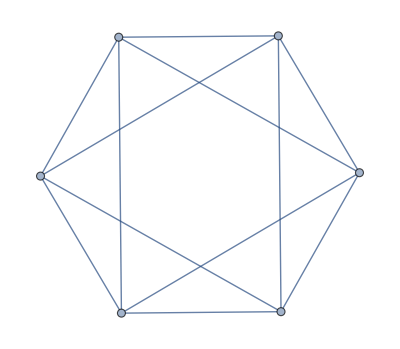
{{-Graphics-,12},{-Graphics-,10},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,10},{-Graphics-,10},{-Graphics-,9},{-Graphics-,9},{-Graphics-,10},{-Graphics-,10},{-Graphics-,9},{-Graphics-,10},{-Graphics-,10},{-Graphics-,11},{-Graphics-,9},{-Graphics-,10},{-Graphics-,9},{-Graphics-,11}}

```mathematica
Block[{order=6,graphs},
graphs=GenerateGraphs[order,2order,4];
Print@ProgressIndicator[Dynamic@gnum,{1,Length@graphs}];
Table[{graphs⟦gnum⟧,Exponent[Expand@EvaluateGraph@graphs⟦gnum⟧,n]},{gnum,Length@graphs}]
]
```

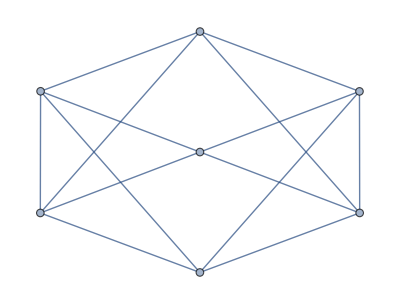
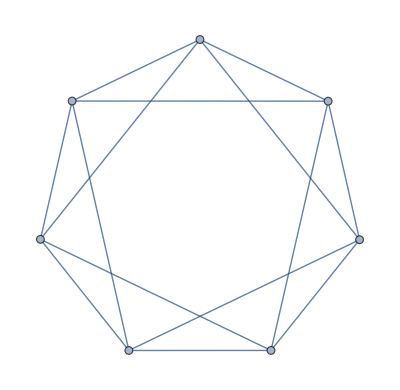
{{-Graphics-,10},{-Graphics-,13},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,10},{-Graphics-,11},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,10},{-Graphics-,11},{-Graphics-,11},{-Graphics-,10},{-Graphics-,10},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,10},{-Graphics-,10},{-Graphics-,12},{-Graphics-,11},{-Graphics-,10},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,10},{-Graphics-,10},{-Graphics-,10},{-Graphics-,11},{-Graphics-,10},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,10},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,9}}

```mathematica
Block[{order=7,graphs},
graphs=GenerateGraphs[order,2order,4];
Print@ProgressIndicator[Dynamic@gnum,{1,Length@graphs}];
Table[{graphs⟦gnum⟧,Exponent[Expand@EvaluateGraph@graphs⟦gnum⟧,n]},{gnum,Length@graphs}]
]
```

```mathematica
Last/@%//Max
```

13

```mathematica
Block[{order=8,graphs},
graphs=GenerateGraphs[order,2order,4];
Print@ProgressIndicator[Dynamic@gnum,{1,Length@graphs}];
Table[{graphs⟦gnum⟧,Exponent[Expand@EvaluateGraph@graphs⟦gnum⟧,n]},{gnum,Length@graphs}]
]
```

{{-Graphics-,15},{-Graphics-,12},{-Graphics-,15},{-Graphics-,13},{-Graphics-,14},{-Graphics-,14},{-Graphics-,14},{-Graphics-,13},{-Graphics-,15},{-Graphics-,14},{-Graphics-,13},{-Graphics-,13},{-Graphics-,12},{-Graphics-,14},{-Graphics-,13},{-Graphics-,13},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,11},{-Graphics-,13},{-Graphics-,11},{-Graphics-,12},{-Graphics-,14},{-Graphics-,14},{-Graphics-,15},{-Graphics-,13},{-Graphics-,14},{-Graphics-,13},{-Graphics-,12},{-Graphics-,11},{-Graphics-,13},{-Graphics-,13},{-Graphics-,13},{-Graphics-,13},{-Graphics-,12},{-Graphics-,14},{-Graphics-,13},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,13},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,14},{-Graphics-,13},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,13},{-Graphics-,12},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,13},{-Graphics-,13},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,12},{-Graphics-,13},{-Graphics-,12},{-Graphics-,13},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,13},{-Graphics-,13},{-Graphics-,13},{-Graphics-,14},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,11},{-Graphics-,14},{-Graphics-,13},{-Graphics-,13},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,13},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,13},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,13},{-Graphics-,13},{-Graphics-,12},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,13},{-Graphics-,11},{-Graphics-,12},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,14},{-Graphics-,12},{-Graphics-,13},{-Graphics-,12},{-Graphics-,11},{-Graphics-,12},{-Graphics-,10},{-Graphics-,12},{-Graphics-,12},{-Graphics-,11},{-Graphics-,13},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,11},{-Graphics-,12}}

```mathematica
Last/@%//Max
```

15

```mathematica
1/n^3{g^2 n^6,g^3 n^6,g^4 n^9,g^5 n^10,g^6 n^12,g^7 n^13,g^8 n^15}/.g->λ n^(-3/2)
```

{λ^2,λ^3/n^(3/2),λ^4,λ^5/(√n),λ^6,λ^7/(√n),λ^8}

```mathematica
RESULTS=Join[%299,%298,%296,%295,%297,%334,%336];
```

```mathematica
First/@Select[RESULTS,Last@#==3+3/2 VertexCount@First@#&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Checking if these graphs are melonic

```mathematica
ClearAll@MyVertexContract;
MyVertexContract[g_Graph,{a_,b_}]:=
Block[{u=FirstCase[EdgeList@g,x_<->a|a<->x_/;x≠b->x],v=FirstCase[EdgeList@g,x_<->b|b<->x_/;x≠a->x]},
Graph@Append[EdgeList@VertexDelete[g,{a,b}],u<->v]
]
```

```mathematica
ClearAll@MelonicGraphQ;
MelonicGraphQ[g_Graph,d_Integer]/;VertexCount@g==2&&EdgeCount@g==d:=LoopFreeGraphQ@g;
MelonicGraphQ[g_Graph,d_Integer]:=
Block[{mellons=Cases[Tally@EdgeList@g,{a_<->b_,d-1}->{a,b}]},
If[mellons=={},
False,
MelonicGraphQ[MyVertexContract[g,First@mellons],d]
]
]
```

```mathematica
MelonicGraphQ[-Graphics-,4]
```

False

```mathematica
Select[Flatten@Import["GraphGames2\\Connected4RegularGraphs.m"],MelonicGraphQ[#,4]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

A figure for the problem statement

```mathematica
Export["MelonicDiagrams.pdf",Row@Select[%51,VertexCount@#≤6&]]
```

MelonicDiagrams.pdf